# Generalized QKT

## Setup

```mathematica
SetDirectory[NotebookDirectory[]];
Get["QKT.wl"];
```

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

## Grid

```mathematica
radius=2;
delta=0.020;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPointsRaw=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
(*Keep only those inside disk*)
region=Select[gridPointsRaw,Norm[#]<radius&];
region//Dimensions
```

{31397,2}

```mathematica
ListPlot[region,AspectRatio->1]
```

## Method

```mathematica
Names["QKT`*"]
```

{Floq,Floqb,Floqbn,Floqn,generateCoherentStateCompiler,generateSpinOperators,MeanLevelSpacingRatio}

```mathematica
(*Floquet parameters*)
J=100;
d=2 J+1;
α=1.099;
(*k=J*2Pi/5.;*)
k=J*Pi(2/5.);
```

```mathematica
ops=generateSpinOperators[J];
```

```mathematica
Print["Generating coherent states over ",Length[region]," points..."];
coherentStateGenerator=generateCoherentStateCompiler[];
statesCompiled=ParallelMap[coherentStateGenerator[J,#[[1]],#[[2]]]&,region,Method->"CoarsestGrained"  (*Optional:better batching*)];
```

Generating coherent states over 31397 points...

```mathematica
Print["Computing Floquet matrix..."];
Clear[mat];
mat=MatrixPower[Floq[J,α,k],5];
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
{eigenvalM,eigenvecM}=Eigensystem[matM,Method->"Direct"];
{eigenvalm,eigenvecm}=Eigensystem[matm,Method->"Direct"];
zerosM=ConstantArray[0.,J];
zerosm=ConstantArray[0.,J+1];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
neweigenval=Riffle[eigenvalM,eigenvalm];
```

Computing Floquet matrix...

```mathematica
sz=ops[[3]];
(*Compute expected values of Sz for each eigenvector*)
szExpectations=Map[#.sz.ConjugateTranspose[#]&,neweigenvec];
(*Get ordering of eigenvectors by increasing<Sz>*)
ordering=Ordering[szExpectations];
(*Sort eigenvectors and expectations accordingly*)
eigenvecsSorted=neweigenvec[[ordering]];
eigenvalSorted=neweigenval[[ordering]];
```

```mathematica
Print["Projecting states into Floquet basis..."];
overlaps=Conjugate[eigenvecsSorted].Transpose[statesCompiled];
Print["Computing IPRs..."];
iprCompiled=Total[Abs[overlaps]^4,{1}];
```

Projecting states into Floquet basis...

Computing IPRs...

```mathematica
newdata=Table[-Log[i]/Log[2 J+1],{i,iprCompiled}];
```

```mathematica
MeanLevelSpacingRatio[eigenvalues_]:=Mean[Min/@Transpose[{#,1/#}]&[Ratios[Differences[Sort[eigenvalues]]]]]
```

```mathematica
{MeanLevelSpacingRatio[Sort[Arg[eigenvalM]]],MeanLevelSpacingRatio[Sort[Arg[eigenvalm]]]}
```

{0.352011,0.365105}

```mathematica
plot=ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],newdata}],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"SunsetColors",PlotLabel->Style["D₂, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],ImageSize->600,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True,InterpolationOrder->3,Background->White]
```

-Graphics-

```mathematica
Export["D2plot.png",plot]
```

D2plot.png

```mathematica
(*Viridis as a pure ColorFunction (no ColorData dependency)*)viridisCF=Function[u,With[{t=Clip[u,{0,1}]},Blend[{RGBColor[68/255,1/255,84/255],RGBColor[72/255,40/255,120/255],RGBColor[62/255,73/255,137/255],RGBColor[49/255,104/255,142/255],RGBColor[38/255,130/255,142/255],RGBColor[31/255,158/255,137/255],RGBColor[53/255,183/255,121/255],RGBColor[110/255,206/255,88/255],RGBColor[181/255,222/255,43/255],RGBColor[253/255,231/255,37/255]},t]]];
```

```mathematica
(*robust range& gentle stretch (all real)*)
{lo,hi}=Quantile[newdata,{0.01,0.99}];
s=(hi-lo)/4.;
stretched=Rescale[ArcSinh[(Clip[newdata,{lo,hi}]-lo)/s]];
```

```mathematica
plot=ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],stretched}],PlotLabel->Style["D₂, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", τ = "<>ToString[N[τ]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],ColorFunction->(viridisCF[#]&),ColorFunctionScaling->False,PlotRange->{0,1},InterpolationOrder->1,AspectRatio->1,Frame->True,FrameLabel->{Style["Q",40],Rotate[Style["P",40],-90 Degree]},PlotLegends->BarLegend[{(viridisCF[#]&),{0,1}}],RegionFunction->Function[{x,y,z},x^2+y^2<=radius^2],ImageSize->1000,PlotTheme->"Detailed",LabelStyle->30];
```

```mathematica
plot=ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],stretched}],PlotLabel->Style["D₂, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", τ = "<>ToString[N[τ]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],ColorFunction->"ThermometerColors",ColorFunctionScaling->False,PlotRange->{0,1},InterpolationOrder->1,AspectRatio->1,Frame->True,FrameLabel->{Style["Q",40],Rotate[Style["P",40],-90 Degree]},PlotLegends->BarLegend[{"ThermometerColors",{0,1}}],RegionFunction->Function[{x,y,z},x^2+y^2<=radius^2],ImageSize->1000,PlotTheme->"Detailed",LabelStyle->30];
```

```mathematica
Export["testb.png",plot]
```

testb.png

```mathematica
husimiValues=Abs[overlaps]^2;
```

```mathematica
q=1;
husimis=Table[husimiValues[[q]]^2,{q,10}];
```

```mathematica
plots=ListDensityPlot[MapThread[Append,{region,Total[husimis[[1;;5]]]}],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["Husimi, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]]<>", Eigenvec_q ="<>ToString[q],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True]
```

-Graphics-

```mathematica
dir="HusimiPlots";
If[!DirectoryQ[dir],CreateDirectory[dir]];
```

```mathematica
husimiValues=Abs[overlaps]^2;
husimiValuesSorted=husimiValues;
```

```mathematica
(*Set parameters*)
numEigenstates=2J+1; 
(*should be 2J+1*)
plots=Table[
Module[{husimiList,plot},
husimiList=MapThread[Append,{region,husimiValuesSorted[[q]]}];
plot=ListDensityPlot[husimiList,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["Husimi, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]]<>", Eigenvec_q = "<>ToString[q],25,Black],ImageSize->1000,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True,InterpolationOrder->1];
Export[FileNameJoin[{dir,"Husimi_J_"<>ToString[J]<>"_q"<>ToString[q]<>".png"}],plot];
plot],{q,1,2J+1,20}];
```

```mathematica
(*Partial husimis*)
plots=Table[
Module[{husimiList,plot},
husimiList=MapThread[Append,{region,Total[husimis[[1;;q]]]}];
plot=ListDensityPlot[husimiList,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["Husimi, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]]<>", Eigenvec_q = "<>ToString[q],25,Black],ImageSize->1000,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True,InterpolationOrder->1];
Export[FileNameJoin[{dir,"Husimi_J_"<>ToString[J]<>"_q"<>ToString[q]<>".png"}],plot];;
plot],{q,2,2J+1}];
```

## Sorting with shannon entropy

```mathematica
Clear[entropy];
entropy[0|0.]=0;
entropy[x_]:=-x*Log[x];
```

```mathematica
shannon=Table[Total[Map[entropy,i]] ,{i,Abs[neweigenvec]^2}];
info=SortBy[Transpose[{Chop[shannon],neweigenvec}],First];
eigenvecsSorted=info[[All,2]];
```

## Cycle γ

```mathematica
zerosM=ConstantArray[0.,J];
zerosm=ConstantArray[0.,J+1];
```

```mathematica
alist=Range[0,Pi,Pi/20.]
```

{0.,0.15708,0.314159,0.471239,0.628319,0.785398,0.942478,1.09956,1.25664,1.41372,1.5708,1.72788,1.88496,2.04204,2.19911,2.35619,2.51327,2.67035,2.82743,2.98451,3.14159}

```mathematica
?Floqb
```

```mathematica
Floqb[j_, α_,k_,γ_]
```

```mathematica
glist=Range[0,1,0.05]
```

{0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.}

```mathematica
dir="HusimiPlots";
If[!DirectoryQ[dir],CreateDirectory[dir]];
```

```mathematica
(*Partial husimis*)
plots=Table[
Module[{matM,matm,eigenvecm,eigenvecM,neweigenvecM,neweigenvecm,neweigenvec,overlaps,iprCompiled,newdata,plot,mat=Floqb[J, alist[[8]],k,γ],lo,hi,s,stretched},
Print["Floquet basis..."];
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
eigenvecM=Orthogonalize[Eigenvectors[matM,Method->"Direct"]];
eigenvecm=Orthogonalize[Eigenvectors[matm,Method->"Direct"]];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
Print["Projecting states into Floquet basis..."];
overlaps=Conjugate[neweigenvec].Transpose[statesCompiled];
Print["Computing IPRs..."];
iprCompiled=Total[Abs[overlaps]^4,{1}];
newdata=Table[-Log[i]/Log[2 J+1],{i,iprCompiled}];
(*plot=ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],newdata}],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BrightBands",PlotLabel->Style["D₂, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", τ = "<>ToString[N[τ]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],ImageSize->600,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True,InterpolationOrder->1];*)

(*robust range & gentle stretch (all real)*)
(*Print["Plotting..."];
{lo,hi}=Quantile[newdata,{0.01,0.99}];
s=(hi-lo)/4.;
stretched=Rescale[ArcSinh[(Clip[newdata,{lo,hi}]-lo)/s]];
plot=ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],stretched}],PlotLabel->Style["D₂, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", τ = "<>ToString[N[τ]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],ColorFunction->"ThermometerColors",ColorFunctionScaling->False,PlotRange->{0,1},InterpolationOrder->1,AspectRatio->1,Frame->True,FrameLabel->{Style["Q",40],Rotate[Style["P",40],-90 Degree]},PlotLegends->BarLegend[{"ThermometerColors",{0,1}}],RegionFunction->Function[{x,y,z},x^2+y^2<=radius^2],ImageSize->1000,PlotTheme->"Detailed",LabelStyle->30];*)
plot=ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],1/iprCompiled}],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"SunsetColors",PlotLabel->Style["D₂, J = "<>ToString[J]<>", α = "<>ToString[N[alist[[8]]]]<>", k = "<>ToString[NumberForm[k,{6,2}]]<>", γ = "<>ToString[N[γ]],25,Black],ImageSize->600,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True,InterpolationOrder->3];

Export[FileNameJoin[{dir,"D2_J_"<>ToString[J]<>"_alpha_"<>ToString[N[alist[[8]]]]<>"_k_"<>ToString[N[k]]<>"_gamma_"<>ToString[γ]<>"_.png"}],plot];
plot]

,{γ,glist}];
```

$Aborted

## Cycle k

```mathematica
zerosM=ConstantArray[0.,J];
zerosm=ConstantArray[0.,J+1];
```

```mathematica
klist=Range[0,Pi*J,Pi/4.];
```

```mathematica
dir="HusimiPlots";
If[!DirectoryQ[dir],CreateDirectory[dir]];
```

```mathematica
k=4*J*Pi(5/6.);
```

```mathematica
alist=Range[0,Pi,Pi/40.];
```

```mathematica
(*Partial husimis*)
plots=Table[
Module[{matM,matm,eigenvecm,eigenvecM,neweigenvecM,neweigenvecm,neweigenvec,overlaps,iprCompiled,newdata,plot,mat=Floq[J, α,k]},
Print["Floquet basis..."];
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
eigenvecM=Orthogonalize[Eigenvectors[matM,Method->"Direct"]];
eigenvecm=Orthogonalize[Eigenvectors[matm,Method->"Direct"]];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
Print["Projecting states into Floquet basis..."];
overlaps=Conjugate[neweigenvec].Transpose[statesCompiled];
Print["Computing IPRs..."];
iprCompiled=Total[Abs[overlaps]^4,{1}];
newdata=Table[-Log[i]/Log[2 J+1],{i,iprCompiled}];

plot=ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],newdata}],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"SunsetColors",PlotLabel->Style["D₂, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True,InterpolationOrder->3];
Export[FileNameJoin[{dir,"D2_J_"<>ToString[J]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[N[k]]<>"_.png"}],plot];
plot]

,{α,alist}];
```

# Symmetric COE

```mathematica
(*Floquet parameters*)
J=100;
a=8/10.;
k=9/10.;
```

```mathematica
ops=generateSpinOperators[J];
```

```mathematica
Jx=ops[[1]];
Jz=ops[[3]];
Ukick=MatrixExp[-I*(k/(2 J))*(Jx.Jx)];
Ufree=MatrixExp[-I*(a/2)*Jz];
matTR=Ufree.Ukick.Ufree;
```

```mathematica
symErr=N@Norm[matTR-Transpose[matTR],"Frobenius"]
```

9.83802×10^-15

```mathematica
vals=Eigenvalues[N[matTR,50]];
N[{vals,Arg[vals]}];
```

```mathematica
{vals,vecs}=Eigensystem[N[matTR]];
```

```mathematica
fixReal[v_,tol_:10^-20]:=Module[{s=v.v,w},
(*v.v is the bilinear form v^T v (no conjugation)*)
If[Abs[s]<tol,w=v+Conjugate[v],
(*fallback if s≈0*)
w=Exp[-I Arg[s]/2] v                
(*phase so that w=w*ideally*)];
Normalize[Chop[w,tol]]];
```

```mathematica
vecsR=fixReal/@vecs;
maxIm=N@Max[Abs[Im[Flatten[vecsR]]]]
```

1.32663×10^-11

```mathematica
V=Transpose[vecsR];          (*eigenvectors as columns*)
(*then:Transpose[V].matTR.V should be diagonal with diagonal=vals*)
```

```mathematica
orthErr=N@Norm[Transpose[V].V-IdentityMatrix[Length[V]],"Frobenius"]
```

4.76958×10^-11

```mathematica
d=Transpose[V].matTR.V;
diagErr=N@Norm[d-DiagonalMatrix[Diagonal[d]],"Frobenius"]
```

4.76955×10^-11

# Texture

```mathematica
(*Floquet parameters*)
J=100;
d=2 J+1;
α=1.099;
k=0.3;
```

```mathematica
Print["Generating coherent states over ",Length[region]," points..."];
coherentStateGenerator=generateCoherentStateCompiler[];
statesCompiled=ParallelMap[coherentStateGenerator[J,#[[1]],#[[2]]]&,region,Method->"CoarsestGrained"  (*Optional:better batching*)];
```

Generating coherent states over 31397 points...

```mathematica
Print["Computing Floquet matrix..."];
Clear[mat];
mat=Floq[J,α,k];
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
{eigenvalM,eigenvecM}=Eigensystem[matM,Method->"Direct"];
{eigenvalm,eigenvecm}=Eigensystem[matm,Method->"Direct"];
zerosM=ConstantArray[0.,J];
zerosm=ConstantArray[0.,J+1];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
neweigenval=Riffle[eigenvalM,eigenvalm];
```

Computing Floquet matrix...

```mathematica
Print["Projecting states into Floquet basis..."];
overlaps=Conjugate[neweigenvec].Transpose[statesCompiled];
Print["Computing IPRs..."];
iprCompiled=Total[Abs[overlaps]^4,{1}];
```

Projecting states into Floquet basis...

Computing IPRs...

```mathematica
newdata=Table[-Log[i]/Log[2 J+1],{i,iprCompiled}];
```

```mathematica
plot=ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],newdata}],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"SunsetColors",PlotLabel->Style["D₂, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],ImageSize->600,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True,InterpolationOrder->3,Background->White]
```

-Graphics-

```mathematica
k=0.1;
α=3;
Clear[mat];
mat=Floq[J,α,k];
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
{eigenvalM,eigenvecM}=Eigensystem[matM,Method->"Direct"];
{eigenvalm,eigenvecm}=Eigensystem[matm,Method->"Direct"];
zerosM=ConstantArray[0.,J];
zerosm=ConstantArray[0.,J+1];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
neweigenval=Riffle[eigenvalM,eigenvalm];
"Computing Floquet matrix..."
f1Ket=Normalize[Total[neweigenvec]];
f1Overlaps=Conjugate[f1Ket].Transpose[statesCompiled];
rugosityCompiled=-Log[Abs[f1Overlaps]^2];
```

Computing Floquet matrix...

```mathematica
ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],Chop[rugosityCompiled]}],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"SunsetColors",PlotLabel->Style["D₂, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],ImageSize->600,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True,InterpolationOrder->3,Background->White]
```

-Graphics-

# Localization

```mathematica
coherentStateGenerator=generateCoherentStateCompiler[];
statesCompiled=ParallelMap[coherentStateGenerator[J,#[[1]],#[[2]]]&,region,Method->"CoarsestGrained"  (*Optional:better batching*)];
```

```mathematica
Clear[mat];
mat=Floq[J,α,k];
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
{eigenvalM,eigenvecM}=Eigensystem[matM,Method->"Direct"];
{eigenvalm,eigenvecm}=Eigensystem[matm,Method->"Direct"];
zerosM=ConstantArray[0.,J];
zerosm=ConstantArray[0.,J+1];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
```

```mathematica
overlaps=Conjugate[neweigenvec].Transpose[statesCompiled];
iprCompiled=Total[Abs[overlaps]^4,{1}];
husimiValues=Abs[overlaps]^2;
```

```mathematica
(*region={{Q1,P1},{Q2,P2},...} are your grid points inside r<=2*)
weights=ConstantArray[4*Pi/Length[region],Length[region]];
pref=(2J+1)/(4*Pi);
```

```mathematica
eps=$MachineEpsilon;
Clear[SWehrl];
SWehrl[k_Integer]:=Module[{Q=husimiValues[[k]]},-pref*Total[weights*Q*Log[Clip[Q,{eps,Infinity}]]]];
```

```mathematica
Clear[SWehrlFromRow];
SWehrlFromRow[Qrow_List]:=Module[{Z=Total[weights*Qrow],Qn},Qn=Qrow/Z;
-pref*Total[weights*Qn*Log[Clip[Qn,{$MachineEpsilon,∞}]]]];
```

```mathematica
normChecks=ParallelTable[pref*Total[weights*i],{i,husimiValues}];
```

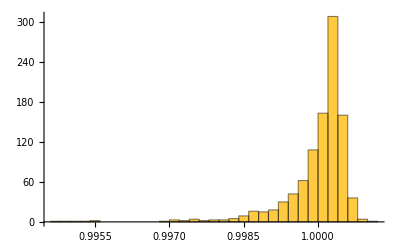

```mathematica
Histogram[normChecks,PlotRange->All]
```

```mathematica
entropies=ParallelMap[SWehrlFromRow,husimiValues];
```

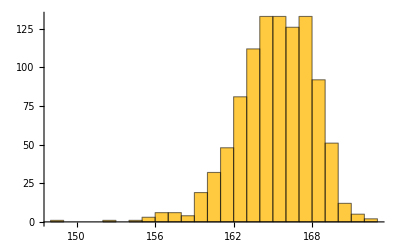

```mathematica
Histogram[entropies,PlotRange->All]
```

```mathematica
perm=Ordering[entropies];
entropiesSorted=entropies[[perm]];
eigenvecsSorted=neweigenvec[[perm]];
overlapsSorted=overlaps[[perm,All]];
husimiValuesSorted=husimiValues[[perm]];
```

```mathematica
info=SortBy[Transpose[{iprCompiled,region}],First];
```

```mathematica
newregion=info[[All,2]];
```

```mathematica
newiprs=info[[All,1]];
```

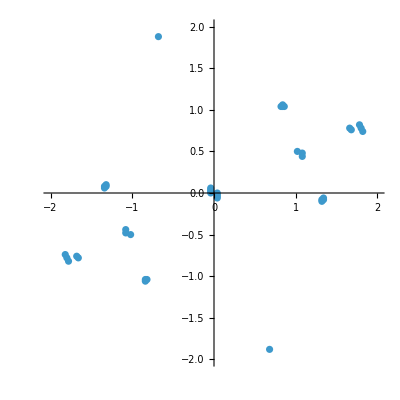

```mathematica
ListPlot[newregion[[-100;;-60]],AspectRatio->1,PlotRange->{{-2,2},{-2,2}}]
```

```mathematica
statesCompiled=ParallelMap[coherentStateGenerator[J,#[[1]],#[[2]]]&,newregion,Method->"CoarsestGrained"  (*Optional:better batching*)];
```

```mathematica
Print["Projecting states into Floquet basis..."];
overlaps=Conjugate[eigenvecsSorted].Transpose[statesCompiled];
```

Projecting states into Floquet basis...

```mathematica
newoverlaps=Transpose[overlaps];
```

```mathematica
plots=Table[ListPlot[Transpose[{Arg[eigenvalSorted],Abs[newoverlaps[[i]]]^2}],PlotRange->All,Filling->Bottom,ImageSize->600,PlotLabel->Style["PR = "<>ToString[1/newiprs[[i]]],20,Black]],{i,-100,-60,1}];
```

```mathematica
ListAnimate[plots,AnimationRunning->False]
```

```mathematica
plots=Table[ListPlot[Transpose[{Arg[eigenvalSorted],Abs[newoverlaps[[i]]]^2}],PlotRange->All,Filling->Bottom,ImageSize->600,PlotLabel->Style["PR = "<>ToString[1/newiprs[[i]]],20,Black]],{i,1,30,1}];
```

```mathematica
ListAnimate[plots,AnimationRunning->False]
```

# Spectrum

## Method

```mathematica
Names["QKT`*"]
```

{Floq,Floqb,Floqbn,Floqn,generateCoherentStateCompiler,generateSpinOperators,MeanLevelSpacingRatio}

```mathematica
(*Floquet parameters*)
J=50;
d=2 J+1;
α=1.099;
(*k=J*2Pi/5.;*)
k=J*Pi(2/5.);
```

```mathematica
ops=generateSpinOperators[J];
```

```mathematica
Print["Computing Floquet matrix..."];
Clear[mat];
mat=Floq[J,α,k];
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
{eigenvalM,eigenvecM}=Eigensystem[matM,Method->"Direct"];
{eigenvalm,eigenvecm}=Eigensystem[matm,Method->"Direct"];
zerosM=ConstantArray[0.,J];
zerosm=ConstantArray[0.,J+1];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
neweigenval=Riffle[eigenvalM,eigenvalm];
```

Computing Floquet matrix...

```mathematica
{MeanLevelSpacingRatio[Sort[Arg[eigenvalM]]],MeanLevelSpacingRatio[Sort[Arg[eigenvalm]]]}
```

{0.211747,0.199212}

```mathematica
alist=Range[0,Pi,Pi/50.];
```

```mathematica
rvalues={};
Do[
mat=Floq[J,a,k];
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
{eigenvalM,eigenvecM}=Eigensystem[matM,Method->"Direct"];
{eigenvalm,eigenvecm}=Eigensystem[matm,Method->"Direct"];
AppendTo[rvalues,{a,Quiet[MeanLevelSpacingRatio[Sort[Arg[eigenvalM]]]],Quiet[MeanLevelSpacingRatio[Sort[Arg[eigenvalm]]]]}];
,{a,alist}];
```

Min::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Min::nord will be suppressed during this calculation.

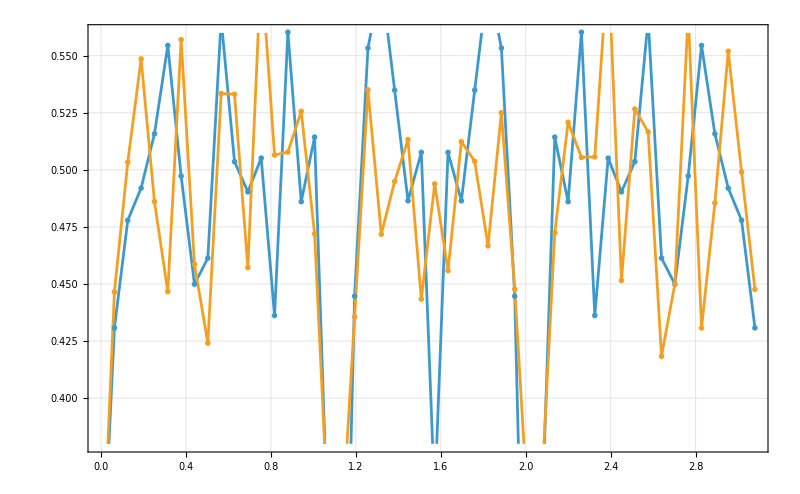

```mathematica
ListPlot[{Transpose[{rvalues[[All,1]],rvalues[[All,2]]}],Transpose[{rvalues[[All,1]],rvalues[[All,3]]}]},PlotTheme->"Detailed",Joined->True,PlotMarkers->"OpenMarkers",ImageSize->800,PlotRange->{All,{0.38,0.56}}]
```

```mathematica
(*Floquet parameters*)
J=100;
d=2 J+1;
α=(2/5.)Pi;
(*k=J*2Pi/5.;*)
k=Pi*J(2/5.);
```

```mathematica
alist=Range[0,Pi,Pi/500];
alist//Length
```

501

```mathematica
levelsm={};
levelsM={};
Do[
mat=Floq[J,a,k];
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
eigenvalM=Eigenvalues[matM,Method->"Direct"];
eigenvalm=Eigenvalues[matm,Method->"Direct"];
AppendTo[levelsM,Transpose[{ConstantArray[a,J+1],Arg[eigenvalM]}]];
AppendTo[levelsm,Transpose[{ConstantArray[a,J],Arg[eigenvalm]}]];
,{a,alist}];
```

```mathematica
p=2;
q=5;
```

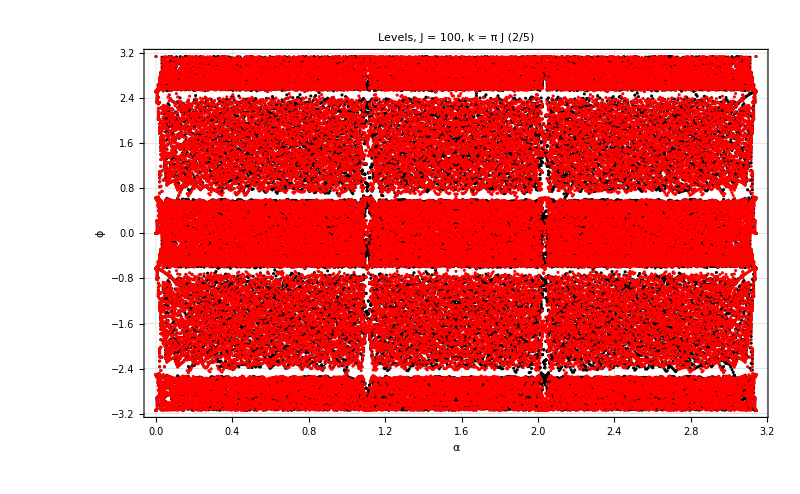

```mathematica
plot2=ListPlot[{Flatten[levelsm,1],Flatten[levelsM,1]},PlotStyle->{Black,Red},PlotRange->All,ImageSize->800,PlotTheme->"Detailed",PlotLabel->Style[Row[{"Levels, J = ",J,", k = π J (",p,"/",q,")"}],25,Black],FrameStyle->Directive[Black,20],FrameLabel->{"α","ϕ"},Background->White]
```

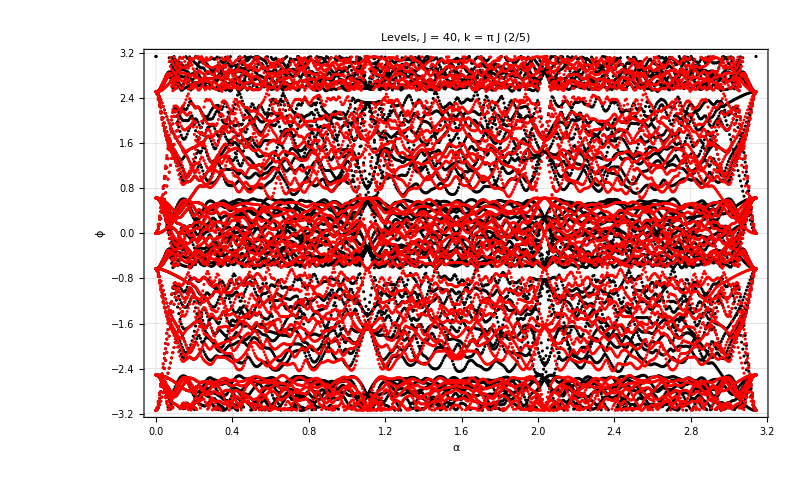

```mathematica
plot2=ListPlot[{Flatten[levelsm,1],Flatten[levelsM,1]},PlotStyle->{Black,Red},PlotRange->All,ImageSize->800,PlotTheme->"Detailed",PlotLabel->Style[Row[{"Levels, J = ",J,", k = π J (",p,"/",q,")"}],25,Black],FrameStyle->Directive[Black,20],FrameLabel->{"α","ϕ"}]
```

```mathematica
Export["test2.png",plot2,ImageResolution->500]
```

test2.png

```mathematica
Export["test1.png",plot1,ImageResolution->500]
```

test1.png

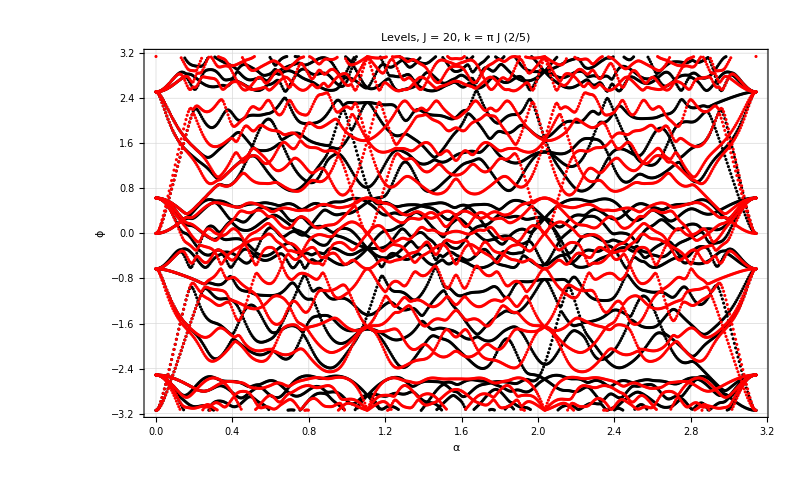

```mathematica
plot1=ListPlot[{Flatten[levelsm,1],Flatten[levelsM,1]},PlotStyle->{Black,Red},PlotRange->All,ImageSize->800,PlotTheme->"Detailed",PlotLabel->Style[Row[{"Levels, J = ",J,", k = π J (",p,"/",q,")"}],25,Black],FrameStyle->Directive[Black,20],FrameLabel->{"α","ϕ"}]
```

```mathematica
J=20;
```

```mathematica
(*1. Generate first 200 rational fractions p/q ordered by denominator*)
rationalFractions={};
q=1;
While[Length[rationalFractions]<20,Do[If[GCD[p,q]==1,AppendTo[rationalFractions,p/q]],{p,1,q}];
q++;];
rationalFractions=Take[rationalFractions,20];
```

```mathematica
alist=Range[0,3.3,1/150.];
alist//Length
```

496

```mathematica
dir="Levels";
If[!DirectoryQ[dir],CreateDirectory[dir]];
```

```mathematica
(*2. Main Workflow*)
plots=Do[
Module[{matM,matm,eigenvecm,eigenvecM,neweigenvecM,neweigenvecm,neweigenvec,overlaps,iprCompiled,newdata,plot,frac=rationalFractions[[i]],mat,q,p},
p=Numerator[frac];
q=Denominator[frac];
k=N[Pi*J*frac];

Print["Processing p = "<>ToString[p]<>", q = "<>ToString[q]<>"..."];
levelsm={};
levelsM={};
Do[
mat=Floq[J,a,k];
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
eigenvalM=Eigenvalues[matM,Method->"Direct"];
eigenvalm=Eigenvalues[matm,Method->"Direct"];
AppendTo[levelsM,Transpose[{ConstantArray[a,J+1],Arg[eigenvalM]}]];
AppendTo[levelsm,Transpose[{ConstantArray[a,J],Arg[eigenvalm]}]];
plot=ListPlot[{Flatten[levelsm,1],Flatten[levelsM,1]},PlotStyle->{Black,Red},PlotRange->All,ImageSize->800,PlotTheme->"Detailed",PlotLabel->Style[Row[{"Levels, J = ",J,", α = ",NumberForm[N[α],{3,2}],", k = π J (",p,"/",q,")"}],25,Black],FrameStyle->Directive[Black,20]];
,{a,alist}];
Export[FileNameJoin[{dir,"levels_J_"<>ToString[J]<>"_k_"<>ToString[NumberForm[N[k],{3,2}]]<>"_p_"<>ToString[p]<>"_q_"<>ToString[q]<>".png"}],plot];

];
,{i,1,Length[rationalFractions]}];
```

Processing p = 1, q = 1...

Processing p = 1, q = 2...

Processing p = 1, q = 3...

Processing p = 2, q = 3...

Processing p = 1, q = 4...

Processing p = 3, q = 4...

Processing p = 1, q = 5...

Processing p = 2, q = 5...

Processing p = 3, q = 5...

Processing p = 4, q = 5...

Processing p = 1, q = 6...

Processing p = 5, q = 6...

Processing p = 1, q = 7...

Processing p = 2, q = 7...

Processing p = 3, q = 7...

Processing p = 4, q = 7...

Processing p = 5, q = 7...

Processing p = 6, q = 7...

Processing p = 1, q = 8...

Processing p = 3, q = 8...